### 3-channel calculation

```mathematica
Vmorse[a_,re_,De_,r_]:=De (1-ⅇ^(-(r-re)/a))^2-De;Vdiag[r_,a_,re_,D11_,D22_,D33_,Eth_]:=({{Vmorse[a,re,D11,r]+Eth[[1]], 0, 0}, {0, Vmorse[a,re,D22,r]+Eth[[2]], 0}, {0, 0, Vmorse[a,re,D33,r]+Eth[[3]]}});
Vcoupling[r_,a_,V12_,V23_,r12_,r23_,a12_,a23_]:=({{0, V12 ⅇ^(-(r-r12)^2/a12^2), 0}, {V12 ⅇ^(-(r-r12)^2/a12^2), 0, V23 ⅇ^(-(r-r23)^2/a23^2)}, {0, V23 ⅇ^(-(r-r23)^2/a23^2), 0}});
```

```mathematica
Vmat[r_,a_,re_,D11_,D22_,D33_,V12_,V23_,r12_,r23_,a12_,a23_,Eth_]:=Vdiag[r,a,re,D11,D22,D33,Eth]+Vcoupling[r,a,V12,V23,r12,r23,a12,a23]
```

```mathematica
Nopen[Emin_,Emax_,Eth_]:=Module[{nmin,nmax},
nmax=Length[Select[Eth,#<Emin &]];
nmin=Length[Select[Eth,#<Emax &]];
If[nmax≠nmin,0,nmin]
]
se[l_,k_,r_]=√(k/π)r SphericalBesselJ[l,k r];
ce[l_,k_,r_]=-√(k/π)r SphericalBesselY[l,k r];
dse[l_,k_,r_]=Simplify[D[se[l,k,r],r]];
dce[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
Setupdiagsc[Ε_,Nopen_,Eth_,r_]:=Module[{ii},
s[Ε,r]=DiagonalMatrix[Table[se[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
c[Ε,r]=DiagonalMatrix[Table[ce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
ds[Ε,r]=DiagonalMatrix[Table[dse[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
dc[Ε,r]=DiagonalMatrix[Table[dce[0,√(Ε-Eth[[ii]]),r],{ii,1,Nopen}]];
{s[Ε,r],c[Ε,r],ds[Ε,r],dc[Ε,r]}
]
```

```mathematica
Nchan=3;
Eth={0.0,3.0,5.0};
a=1;
re=1;
l=0;
rmin=0.0;
rmax=12.0;
D11=1.0;
D22=4.0;
D33=6.0;
V12=0.2;
V23=0.2;
r12=0.5;
r23=1.0;
a12=0.5;
a23=0.5;
no=1;
Erange=Which[
no==1,{Eth[[1]]+0.001,Eth[[2]]-0.001},
no==2,{Eth[[2]]+0.001,Eth[[3]]-0.001},
no==3,{Eth[[3]]+0.001,Eth[[3]]+10.0}];
VV[r_]=Vmat[r,a,re,D11,D22,D33,V12,V23,r12,r23,a12,a23,Eth];
```

```mathematica
VV[x]//MatrixForm
```

(-1.+1. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-0.5+x)^2) | 0
0.2 ⅇ^(-4. (-0.5+x)^2) | -1.+4. (1-ⅇ^(1-x))^2 | 0.2 ⅇ^(-4. (-1.+x)^2)
0 | 0.2 ⅇ^(-4. (-1.+x)^2) | -1.+6. (1-ⅇ^(1-x))^2)

```mathematica
diagsc=Setupdiagsc[Ε,no,Eth,r];
```

```mathematica
eqs[Ε_,r_,u_,Vmat_,Nchan_]:=Table[-Subscript[u, i,α]''[r]+Sum[VV[r][[i,j]]Subscript[u, j,α][r],{j,1,Nchan}]-Ε Subscript[u, i,α][r]==0,{i,1,Nchan},{α,1,Nchan}];
(*boundarycond[Ε_,rmin_,rmax_,Eth_,Nchan_,u_]:=Module[{},
Table[{
Subscript[u, ii,β][rmin]==0,
With[{i=ii,α=β},If[Ε<Eth[[i]],
Subscript[u, i,α][rmax]==0,
Subscript[u, i,α]'[rmin]==KroneckerDelta[i,α]]]},
{ii,1,Nchan},{β,1,Nchan}]
];*)
boundarycond[Ε_,rmin_,rmax_,Eth_,Nchan_,u_]:=Module[{},
Table[{
Subscript[u, ii,β][rmin]==0,
With[{i=ii,α=β},
Subscript[u, i,α]'[rmin]==KroneckerDelta[i,α]]},
{ii,1,Nchan},{β,1,Nchan}]
];
```

```mathematica
alleqs[Ε_,r_,rmin_,rmax_,Eth_,Nchan_,u_,Vmat_]:=Table[Flatten[{Transpose[eqs[Ε,r,u,Vmat,Nchan]][[i]],Transpose[boundarycond[Ε,rmin,rmax,Eth,Nchan,u]][[i]]}],{i,1,Nchan}];
```

```mathematica
Etest=Erange[[1]]+0.01;
equations=alleqs[Etest,r,rmin,rmax,Eth,Nchan,u,VV[r]];
```

```mathematica
umat=Table[Subscript[u, i,j][r],{i,1,Nchan},{j,1,Nchan}];
```

```mathematica
NDSolve[equations[[1]],umatᵀ[[1]],{r,rmin,rmax},Method->{"Automatic"}]
```

{{u_(1,1)[r]→InterpolatingFunction[…][r],u_(2,1)[r]→InterpolatingFunction[…][r],u_(3,1)[r]→InterpolatingFunction[…][r]}}

```mathematica
sols=Flatten[Table[NDSolve[equations[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,Nchan}]];
k=Table[√(Etest-Eth[[i]]),{i,1,no}];
```

```mathematica
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
```

```mathematica
uopen[[1]]
```

{InterpolatingFunction[…][r]}

```mathematica
Unprotect[Kmatrix];Kmatrix[Eth_,nchan_,no_,r_,rmin_,rmax_,Vmat_,Ε_]:=Module[{K,Imat,Jmat,sols,eqs,uopen,umat,u,i,j,α,β,diagsc,S},
diagsc=Setupdiagsc[Ε,no,Eth,r];
umat=Table[Subscript[u, i,j][r],{i,1,nchan},{j,1,nchan}];
eqs=alleqs[Ε,r,rmin,rmax,Eth,nchan,u,Vmat];
sols=Flatten[Table[NDSolve[eqs[[α]],umatᵀ[[α]],{r,rmin,rmax},Method->{"Automatic"}],{α,1,nchan}]];
uopen=Table[umat[[i,α]]/.sols,{i,1,no},{α,1,no}];
Imat=Table[Wronskian[{uopen[[i,β]],diagsc[[2,i,i]]},r]/Wronskian[{diagsc[[1,i,i]],diagsc[[2,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;Jmat=Table[Wronskian[{uopen[[i,β]],diagsc[[1,i,i]]},r]/Wronskian[{diagsc[[2,i,i]],diagsc[[1,i,i]]},r],{i,1,no},{β,1,no}]/.r->rmax;
K=Jmat.Inverse[Imat]/.r->rmax;
S=(IdentityMatrix[no]+ⅈ K).Inverse[IdentityMatrix[no]-ⅈ K];
{K,S}
]
Protect[Kmatrix];
```

```mathematica
Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]
```

{{{-0.40484}},{{0.718367-0.695664 ⅈ}}}

```mathematica
δ[De_,Ε_]:=Arg[Hypergeometric1F1[1/2+ⅈ √Ε-√(a^2 De),1+2ⅈ √Ε,2 ⅇ^(re/a)√(a^2 De)]]
```

```mathematica
dat=Table[{Etest,Kmatrix[Eth,Nchan,no,r,rmin,rmax,VV[r],Etest]},{Etest,Erange[[1]],Erange[[2]],0.002}];
```

```mathematica
dat[[1]]
```

{0.001,{{{-0.118236}},{{0.972426-0.233213 ⅈ}}}}

```mathematica
K11=Table[{dat[[n,1]],dat[[n,2,1,1,1]]},{n,1,Length[dat]}];
(*K12=Table[{dat[[n,1]],dat[[n,2,2]]},{n,1,Length[dat]}];
K21=Table[{dat[[n,1]],dat[[n,2,3]]},{n,1,Length[dat]}];
K22=Table[{dat[[n,1]],dat[[n,2,4]]},{n,1,Length[dat]}];*)
```

```mathematica
K11[[1]]
```

{0.001,-0.118236}

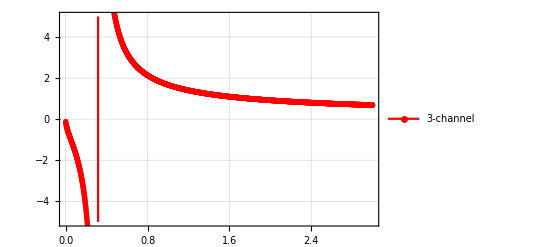

```mathematica
KK=ListPlot[Legended[K11,"3-channel"],Joined->True,Frame->True,PlotStyle->Red,GridLines->Automatic,PlotRange->{-5,5}]
```

```mathematica
De=6;a=1;re=1;
l=0;rmin=0;rmax=20;{vals,funs}=NDEigensystem[{-D[u[r],{r,2}]+(Vmorse[a,re,De,r]+De+(l(l+1))/r^2)u[r],DirichletCondition[u[r]==0,r==rmin],DirichletCondition[u[r]==0,r==rmax]},u[r],{r,rmin,rmax},3,Method->{"SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.2}}}];
channel3states=vals-De+Eth[[3]]
```

{1.25722,4.15818,5.01988}

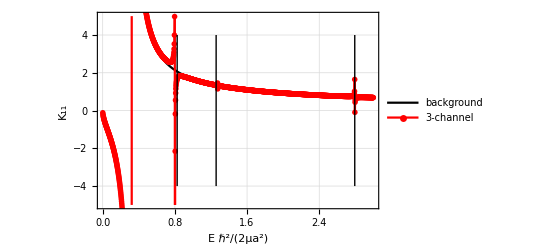

```mathematica
pm=Show[Plot[Legended[Tan[δ[1,Ε]],"background"],{Ε,0.01,2.0},PlotStyle->Black],KK,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_11"} ,Epilog->{Style[Line[{{0.825315,-4},{0.825315,4}}],Dashed],Style[Line[{{1.257222782,-4},{1.257222782,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

From the fortran code (!):

```mathematica
datf=Import["/Users/niravmehta/Documents/GitHub/R-matrix-prop/fort.10"];
```

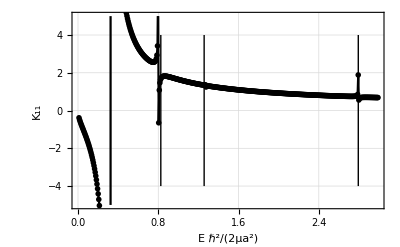

```mathematica
pf=ListPlot[Table[{datf[[i,1]],datf[[i,2]]},{i,1,Length[datf]}],Joined->True,PlotRange->{-5,5},Frame->True,LabelStyle->Large,GridLines->Automatic,FrameLabel->{"Ε ℏ^2/(2μa^2)","K_11"} ,Epilog->{Style[Line[{{0.825315,-4},{0.825315,4}}],Dashed],Style[Line[{{1.257222782,-4},{1.257222782,4}}],Dashed],Style[Line[{{2.79355,-4},{2.79355,4}}],Dashed]}]
```

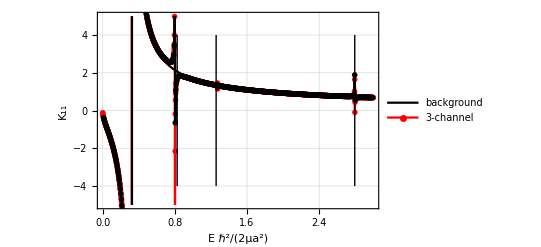

```mathematica
Show[pm,pf]
```